# Assembly Equation and Numerical Solution to Discovery and Production Kinetics

#### Abhishek Sharma Cronin Lab University of Glasgow

NOTE: Some variable names might be different in the manuscript and Mathematica Notebooks.

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/

## Assembly for Isolated Contingent Chain

The Assembly Equation without and with normalization along an isolated assembly path is given by,

								A=∑_(i=1)^N ⅇ^a_i(n_i-1)
								
								A=∑_(i=1)^N ⅇ^(a_i-a_ch)((n_i-1)/n_T)
								
Consider a process where, a fraction (α) of objects combines with the fundamental particles to move to higher assemblies. So, at each assembly step, the copy number at an assembly a_i  is given by, n_i=(1-α)n_i+α n_(i-1).

If the fraction α is constant and independent of the assembly step (which is equivalent to assembly index here), the Assembly of the overall ensemble with assembly step can be estimated as,

```mathematica
N0=10^12; (* Initial Number of Fundamental Particles *)
```

```mathematica
AssemblyCalculate[{aMax_,maxSteps_,α_}]:=Module[{assemblyList,rule,copyNumber,Assembly},assemblyList=Table[ToExpression["N"<>ToString[a]],{a,0,aMax}];
rule=Table[ToExpression["N"<>ToString[a]]->0,{a,1,aMax}];
assemblyList=assemblyList/.rule ;
copyNumber=Table[assemblyList=FullSimplify[Table[If[i==1,(1-α)assemblyList[[i]],(1-α)assemblyList[[i]]+α assemblyList[[i-1]]],{i,1,Length@assemblyList}]],{j,maxSteps}];
Assembly=Table[Total[Table[ⅇ^i If[copyNumber[[j]][[i]]>=1,((copyNumber[[j]][[i]]-1)/FullSimplify[Total@copyNumber[[j]]]),0],{i,Length@copyNumber[[j]]}]],{j,Length@copyNumber}]]
```

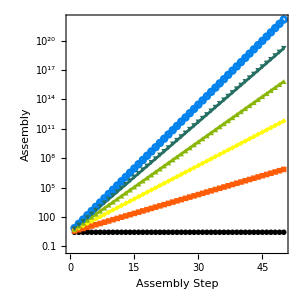

```mathematica
ListLogPlot[Table[AssemblyCalculate[{100,50,α}],{α,0,1,0.2}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,Scaled[0.02]},PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Assembly Step","Assembly"},AspectRatio->1,ImageSize->300]
```

In  another case, we assume that the α depends on assembly step and with increase in assembly step α_s=α_0 f^s, where α_s represents assembly at step s and f is the reduction factor. In this case, the Assembly of the ensemble is given by,

```mathematica
N0=10^12; (* Initial Number of Fundamental Particles *)
```

```mathematica
AssemblyCalculate[{aMax_,maxSteps_,α_,fac_}]:=Module[{assemblyList,rule,αList,copyNumber,Assembly},
assemblyList=Table[ToExpression["N"<>ToString[a]],{a,0,aMax}];
rule=Table[ToExpression["N"<>ToString[a]]->0,{a,1,aMax}];
assemblyList=assemblyList/.rule ;
αList=Table[α fac^(i-1),{i,aMax+1}];
copyNumber=Table[assemblyList=FullSimplify[Table[If[i==1,(1-αList[[i]])assemblyList[[i]],(1-αList[[i]])assemblyList[[i]]+αList[[i-1]] assemblyList[[i-1]]],{i,1,Length@assemblyList}]],{j,maxSteps}];
Assembly=Table[FullSimplify[Total@Table[ⅇ^i If[copyNumber[[j]][[i]]>1,((copyNumber[[j]][[i]]-1)/FullSimplify[Total@copyNumber[[j]]]),0],{i,Length@copyNumber[[j]]}]],{j,Length@copyNumber}]]
```

Case 1: when reduction factor f=1 (which is same as the previous case)

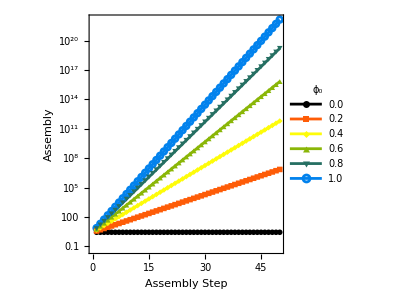

```mathematica
p1=ListLogPlot[Table[AssemblyCalculate[{100,50,α,1.0}],{α,0,1,0.2}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,Scaled[0.02]},PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,PlotLegends->Placed[LineLegend[{"0.0","0.2","0.4","0.6","0.8","1.0"},LegendLabel->"ϕ_0",Spacings->0.2],{0.2,0.7}],FrameLabel->{"Assembly Step","Assembly"},AspectRatio->1,ImageSize->300]
```

Case 2: when reduction factor f=0.33

```mathematica
N0=10^12;
```

General::munfl: 2.81202×10^-18 1.12679×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.81202×10^-18 4.02282×10^-298 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.81202×10^-18 7.38074×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

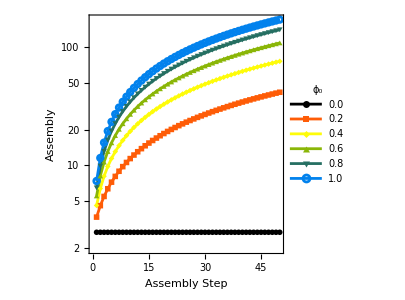

```mathematica
p2=ListLogPlot[Table[AssemblyCalculate[{100,50,α,0.33}],{α,0,1,0.2}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,Scaled[0.02]},PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,PlotLegends->Placed[LineLegend[{"0.0","0.2","0.4","0.6","0.8","1.0"},LegendLabel->"ϕ_0",Spacings->0.2],{0.8,0.33}],FrameLabel->{"Assembly Step","Assembly"},AspectRatio->1,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"AssemblyCalculate_1.png",p1,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyCalculate_1.png

```mathematica
Export[baseDirectory<>"AssemblyCalculate_1.svg",p1]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyCalculate_1.svg

```mathematica
Export[baseDirectory<>"AssemblyCalculate_2.png",p2,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyCalculate_2.png

```mathematica
Export[baseDirectory<>"AssemblyCalculate_2.svg",p2]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyCalculate_2.svg

## Unique Objects in Joint Assembly Space

The number of unique objects from the forward process discovery equation is given by (assuming P_0=1),

```mathematica
Clear[κ,α]
```

```mathematica
nObj[a_,α_,κ_,t_]:=(P0^(α^a)( ∏_(j=1)^(a-1) (∑_(k=0)^(a-1-j) α^k)^(-α^j) )(t κ)^(∑_(k=0)^(a-1) α^k))/(∑_(k=0)^(a-1) α^k) /.P0->1
```

The ratio of the number of unique objects at assembly a and a-1 is given by,

```mathematica
ratio[a_,α_,κ_,t_]:=nObj[a,α,κ,t]/nObj[a-1,α,κ,t]
```

When α=1,

```mathematica
t/.First@Solve[FullSimplify[nObj[a,1,κ,t]/nObj[a-1,1,κ,t]]==1,t]
```

a/κ

Finding the time points when the ratio = 1 for each assembly index.

```mathematica
ratioList[{α_,κ_,t_}]=Table[ratio[a,α,κ,t],{a,2,25}];
```

```mathematica
p1=MapThread[{#1,#2}&,{Range[2,25],Flatten[t/.Solve[#==1]&/@(ratioList[{0.01,κ,t}]/.κ->1 10^-4)]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{2,27048.1},{3,72796.5},{4,195913.},{5,527247.},{6,1.41895×10^6},{7,3.8179×10^6},{8,1.03629×10^7},{9,1.},{10,0.},{11,0.},{12,0.},{13,1.},{14,1.},{15,1.},{16,1.},{17,t},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,t}}

```mathematica
p2=MapThread[{#1,#2}&,{Range[2,25],Flatten[t/.Solve[#==1]&/@(ratioList[{0.2,κ,t}]/.κ->1 10^-4)]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{2,24883.2},{3,56482.9},{4,126191.},{5,281060.},{6,625607.},{7,1.39236×10^6},{8,3.09877×10^6},{9,6.89644×10^6},{10,1.53483×10^7},{11,3.41583×10^7},{12,7.60207×10^7},{13,1.69187×10^8},{14,3.76533×10^8},{15,8.37989×10^8},{16,1.86497×10^9},{17,4.15069×10^9},{18,9.23837×10^9},{19,2.05591×10^10},{20,4.5582×10^10},{21,1.00847×10^11},{22,2.67119×10^11},{23,1.99699×10^12},{24,1.},{25,1.}}

```mathematica
p3=MapThread[{#1,#2}&,{Range[2,25],Flatten[t/.Solve[#==1]&/@(ratioList[{0.5,κ,t}]/.κ->1 10^-4)]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{2,22500.},{3,41684.},{4,72389.5},{5,122327.},{6,204120.},{7,338539.},{8,559805.},{9,924319.},{10,1.52506×10^6},{11,2.51533×10^6},{12,4.14783×10^6},{13,6.83924×10^6},{14,1.12765×10^7},{15,1.85923×10^7},{16,3.06538×10^7},{17,5.05399×10^7},{18,8.33264×10^7},{19,1.37382×10^8},{20,2.26505×10^8},{21,3.73444×10^8},{22,6.15705×10^8},{23,1.01513×10^9},{24,1.67366×10^9},{25,2.7594×10^9}}

```mathematica
p4=MapThread[{#1,#2}&,{Range[2,25],Flatten[t/.Solve[#==1]&/@(ratioList[{0.8,κ,t}]/.κ->1 10^-4)]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{2,20849.3},{3,33537.},{4,48651.8},{5,66813.9},{6,88745.1},{7,115310.},{8,147557.},{9,186758.},{10,234466.},{11,292573.},{12,363391.},{13,449739.},{14,555063.},{15,683567.},{16,840390.},{17,1.03181×10^6},{18,1.26547×10^6},{19,1.55076×10^6},{20,1.89908×10^6},{21,2.32442×10^6},{22,2.84381×10^6},{23,3.47808×10^6},{24,4.25268×10^6},{25,5.19867×10^6}}

```mathematica
p5=MapThread[{#1,#2}&,{Range[2,25],Flatten[t/.Solve[#==1]&/@(ratioList[{0.999999,κ,t}]/.κ->1 10^-4)]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{2,20000.},{3,30000.},{4,40000.},{5,50000.1},{6,60000.1},{7,70000.1},{8,80000.2},{9,90000.3},{10,100000.},{11,110000.},{12,120001.},{13,130001.},{14,140001.},{15,150001.},{16,160001.},{17,170001.},{18,180001.},{19,190001.},{20,200002.},{21,210002.},{22,220002.},{23,230002.},{24,240002.},{25,250003.}}

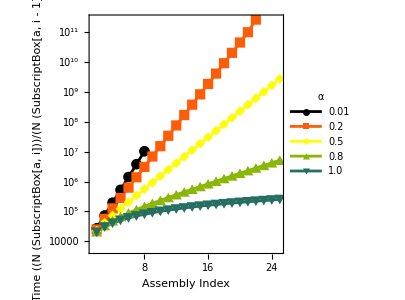

```mathematica
ListLogPlot[{p1[[1;;7]],p2[[1;;21]],p3,p4,p5},PlotMarkers->Automatic,Joined->True,PlotRange->Full,AspectRatio->1,PlotStyle->ColorData[3,"ColorList"],PlotLegends->Placed[LineLegend[{"0.01","0.2","0.5","0.8","1.0"},LegendLabel->"α",Spacings->0.2],{0.2,0.75}],AspectRatio->1,Frame->True,FrameLabel->{"Assembly Index","Time ((N (SubscriptBox[a, i]))/(N (SubscriptBox[a, i - 1]))=1)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

## Numerical Solution to Discovery-Production Dynamics

Calculating Discovery and Production kinetics at different α values, for details see AssemblyTheory_Scaling.nb

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/

```mathematica
nObj[a_,α_,κ_,t_]:=(P0^(α^a)( ∏_(j=1)^(a-1) (∑_(k=0)^(a-1-j) α^k)^(-α^j) )(t κ)^(∑_(k=0)^(a-1) α^k))/(∑_(k=0)^(a-1) α^k) /.P0->1
```

```mathematica
eqns[a_,α_,t0_]:= {D[ToExpression["N"<>ToString[a]][t],t]==-(kF β^a+If[a==0,0,κ(If[a==1,1,(nObj[a-1,α,κ,t])^α]/nObj[a,α,κ,t])]) ToExpression["N"<>ToString[a]][t]+ kF β^(a-1)If[a==0,0,If[a==1,1,nObj[a-1,α,κ,t]]/nObj[a,α,κ,t]]ToExpression["N"<>ToString[a-1]],ToExpression["N"<>ToString[a]][t0]==If[a==0,NI,0]};
```

```mathematica
NI=1 10^12;β=0.5;κ=1 10^-4;kF=1 10^-5; (* Simulation Parameters as used previously *)
```

```mathematica
solveEquations[{α_,aMax_,tMax_,maxStepSize_}]:=Module[{out},
out=Table[Evaluate[ToExpression["sol"<>ToString[a]]]=First@Monitor[NDSolve[eqns[a,α,1 10^-3],ToExpression["N"<>ToString[a]][t],{t,1 10^-3,tMax},WorkingPrecision->MachinePrecision,PrecisionGoal->10,AccuracyGoal->10,MaxSteps->10^15,MaxStepSize->maxStepSize,EvaluationMonitor:>(step=t)],step];Evaluate[ToExpression["N"<>ToString[a]]]=FullSimplify[ToExpression["N"<>ToString[a]][t]/.Evaluate[ToExpression["sol"<>ToString[a]]]],{a,0,aMax}];
Return[out]]
```

Solving equations with different α values, max assembly 25 and total steps 10^9. This step will take time!

```mathematica
totalTime=10^9; (* Total time *)
```

```mathematica
threshold=10; (* Threshold time for object detection *)
```

It is important to note that, the copy numbers have no meaning until the number of discovered objects >= 1. So, once we have solved the equations, we will only plot the copy numbers when the minimum number of unique objects is 1. Here, as the initial plotting time, we use the initial plotting time defined by the maximum time required for discovering one object in  the assembly index range 1-25.

#### Case 1: α=1.0

```mathematica
Clear[#]&/@Table["N"<>ToString[a],{a,0,25}];Clear[#]&/@Table["sol"<>ToString[a],{a,0,25}];Clear[α];
out1=solveEquations[{1.0,25,totalTime,10^3}];
```

```mathematica
solnList=ToExpression["N"<>ToString[#]]&/@Range[1,25];
```

```mathematica
posPlot1=Flatten@Table[Block[{maxPos,val,pos},func[t_]=solnList[[i]];
maxPos=First@@Position[func["ValuesOnGrid"],Max[func["ValuesOnGrid"]]];
val=First@Nearest[func["ValuesOnGrid"][[1;;maxPos]],threshold];pos=Flatten@Position[func["ValuesOnGrid"],val];Flatten[func["Coordinates"]][[pos]]],{i,Length@solnList}];
```

```mathematica
tDis=Table[f[t_]=nObj[a,1.0,κ,t];t/.First@Solve[f[t]==1,t,Assumptions->{t>0&&t∈Reals}],{a,1,25}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Max@tDis
```

101771.

```mathematica
Position[Table[tDis[[i]]<posPlot1[[i]],{i,Length@posPlot1}],True]
```

{}

```mathematica
thresholdList1={}
```

{}

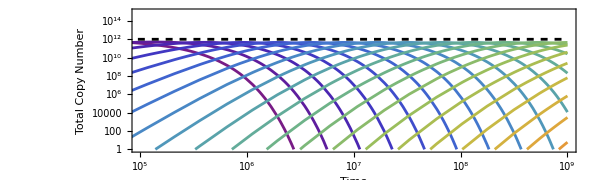

```mathematica
p11=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->1.0],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->1.0],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

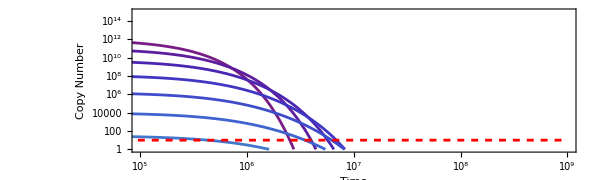

```mathematica
p12=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}],LogLogPlot[threshold,{t,0.001,totalTime},PlotStyle->{Red,Dashed},PlotRange->{{Max@tDis,10^9},{1,10^15}},AspectRatio->0.3],ListLogLogPlot[Evaluate[{#,threshold}&/@posPlot1[[1;;5]]],PlotStyle->{Red,PointSize[0.01]},Filling->Axis]},ImageSize->600]
```

```mathematica
colorStyle=Opacity[0.2,#]&/@Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]};
```

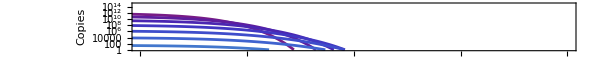

```mathematica
p13=LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha1.0_LongTime.png",p11,ImageResolution->300]; 
Export[baseDirectory<>"CopyNumber_alpha1.0_LongTime.png",p12,ImageResolution->300];
Export[baseDirectory<>"CopyNumber_alpha1.0_LongTime2.png",p13,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha1.0_LongTime.svg",p11]; 
Export[baseDirectory<>"CopyNumber_alpha1.0_LongTime.svg",p12];
Export[baseDirectory<>"CopyNumber_alpha1.0_LongTime2.svg",p13];
```

```mathematica
α=1.0;Table[ToExpression["n"<>ToString[a]][t_]=ToExpression["N"<>ToString[a]],{a,0,25}];
```

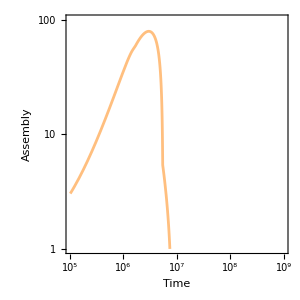

```mathematica
p1=LogLogPlot[Total@Table[ⅇ^a((If[a==0,1,nObj[a,α,κ,t]]With[{p=ToExpression["n"<>ToString[a]][t]},If[p>1,p-1,0]])/Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]],{a,0,25}]]),{a,0,25}],{t,Max@tDis,totalTime},Frame->True,FrameLabel->{"Time","Assembly"},AspectRatio->1,PlotStyle->{Orange,Opacity[0.5]},PlotRange->{{Max@tDis,10^9},{1,10^2}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

#### Case 2: α=0.8

```mathematica
Clear[#]&/@Table["N"<>ToString[a],{a,0,25}];Clear[#]&/@Table["sol"<>ToString[a],{a,0,25}];Clear[α];
out2=solveEquations[{0.8,25,totalTime,10^5}];
```

```mathematica
solnList=ToExpression["N"<>ToString[#]]&/@Range[1,25];
```

```mathematica
tDis=Table[f[t_]=nObj[a,0.8,κ,t];t/.First@Solve[f[t]==1,t,Assumptions->{t>0&&t∈Reals}],{a,1,25}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Max@tDis
```

48940.8

```mathematica
posPlot2=Flatten@Table[Block[{maxPos,val,pos},func[t_]=solnList[[i]];
maxPos=First@@Position[func["ValuesOnGrid"],Max[func["ValuesOnGrid"]]];
val=First@Nearest[func["ValuesOnGrid"][[1;;maxPos]],threshold];pos=Flatten@Position[func["ValuesOnGrid"],val];Flatten[func["Coordinates"]][[pos]]],{i,Length@solnList}];
```

```mathematica
Flatten@Position[Table[tDis[[i]]<posPlot2[[i]],{i,Length@posPlot2}],True]
```

{7,8,9,10,11,12,13,14,15,16,17}

```mathematica
thresholdList2={{7,posPlot2[[7]]}}
```

{{7,290479.}}

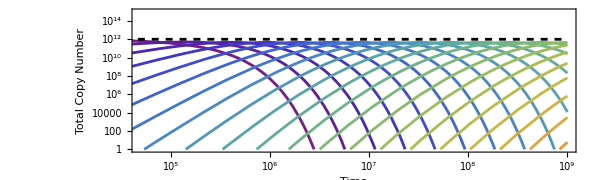

```mathematica
p21=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.8],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.8],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

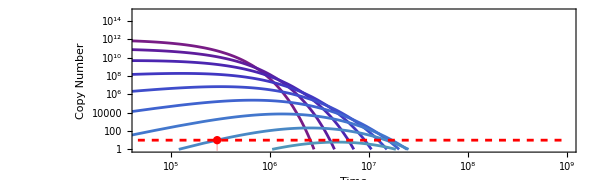

```mathematica
p22=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}],LogLogPlot[threshold,{t,0.001,totalTime},PlotStyle->{Red,Dashed},PlotRange->{{Max@tDis,10^9},{1,10^15}},AspectRatio->0.3],ListLogLogPlot[Evaluate[{#,threshold}&/@posPlot2[[1;;7]]],PlotStyle->{Red,PointSize[0.01]},Filling->Axis]},ImageSize->600]
```

```mathematica
colorStyle=Opacity[0.2,#]&/@Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]};
```

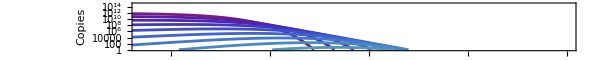

```mathematica
p23=LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.8_LongTime.png",p21,ImageResolution->300]; 
Export[baseDirectory<>"CopyNumber_alpha0.8_LongTime.png",p22,ImageResolution->300];
Export[baseDirectory<>"CopyNumber_alpha0.8_LongTime2.png",p23,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.8_LongTime.svg",p21]; 
Export[baseDirectory<>"CopyNumber_alpha0.8_LongTime.svg",p22];
Export[baseDirectory<>"CopyNumber_alpha0.8_LongTime2.svg",p23];
```

```mathematica
α=0.8;Table[ToExpression["n"<>ToString[a]][t_]=ToExpression["N"<>ToString[a]],{a,0,25}];
```

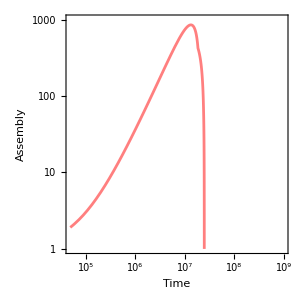

```mathematica
p2=LogLogPlot[Total@Table[ⅇ^a((If[a==0,1,nObj[a,α,κ,t]]With[{p=ToExpression["n"<>ToString[a]][t]},If[p>1,p-1,0]])/Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]],{a,0,25}]]),{a,0,25}],{t,Max@tDis,totalTime},Frame->True,FrameLabel->{"Time","Assembly"},AspectRatio->1,PlotStyle->{Red,Opacity[0.5]},PlotRange->{{Max@tDis,10^9},{1,10^3}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

#### Case 3: α=0.5

```mathematica
Clear[#]&/@Table["N"<>ToString[a],{a,0,25}];Clear[#]&/@Table["sol"<>ToString[a],{a,0,25}];Clear[α];
out3=solveEquations[{0.5,25,totalTime,10^5}];
```

```mathematica
solnList=ToExpression["N"<>ToString[#]]&/@Range[1,25];
```

```mathematica
tDis=Table[f[t_]=nObj[a,0.5,κ,t];t/.First@Solve[f[t]==1,t,Assumptions->{t>0&&t∈Reals}],{a,1,25}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Max@tDis
```

20000.

```mathematica
posPlot3=Flatten@Table[Block[{maxPos,val,pos},func[t_]=solnList[[i]];
maxPos=First@@Position[func["ValuesOnGrid"],Max[func["ValuesOnGrid"]]];
val=First@Nearest[func["ValuesOnGrid"][[1;;maxPos]],threshold];pos=Flatten@Position[func["ValuesOnGrid"],val];Flatten[func["Coordinates"]][[pos]]],{i,Length@solnList}];
```

```mathematica
Flatten@Position[Table[tDis[[i]]<posPlot3[[i]],{i,Length@posPlot3}],True]
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
posPlot3
```

{0.001,0.00100267,0.0500226,99.7076,3505.07,29273.7,131565.,431425.,1.24057×10^6,3.37394×10^6,9.07404×10^6,2.4779×10^7,6.9979×10^7,2.11979×10^8,7.53279×10^8,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,9.99939×10^8,0.001,0.001,0.001,0.001}

```mathematica
thresholdList3=MapThread[{#1,#2}&,{Range[6,15],posPlot3[[6;;15]]}]
```

{{6,29273.7},{7,131565.},{8,431425.},{9,1.24057×10^6},{10,3.37394×10^6},{11,9.07404×10^6},{12,2.4779×10^7},{13,6.9979×10^7},{14,2.11979×10^8},{15,7.53279×10^8}}

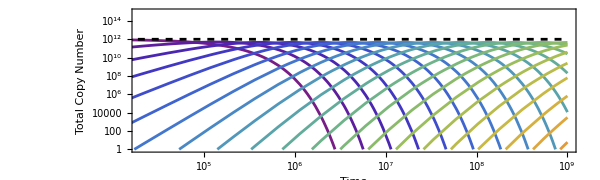

```mathematica
p31=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.5],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.5],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

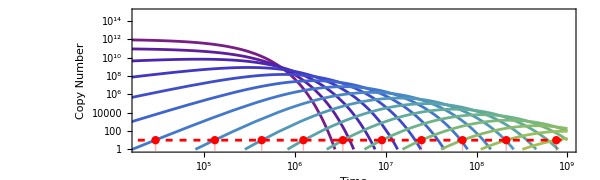

```mathematica
p32=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}],LogLogPlot[threshold,{t,0.001,totalTime},PlotStyle->{Red,Dashed},PlotRange->{{Max@tDis,10^9},{1,10^15}},AspectRatio->0.3],ListLogLogPlot[Evaluate[{#,threshold}&/@posPlot3[[6;;15]]],PlotStyle->{Red,PointSize[0.01]},Filling->Axis]},ImageSize->600]
```

```mathematica
colorStyle=Opacity[0.2,#]&/@Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]};
```

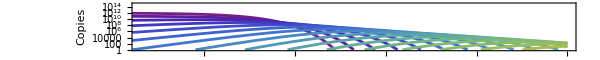

```mathematica
p33=LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.5_LongTime.png",p31,ImageResolution->300]; 
Export[baseDirectory<>"CopyNumber_alpha0.5_LongTime.png",p32,ImageResolution->300];
Export[baseDirectory<>"CopyNumber_alpha0.5_LongTime2.png",p33,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.5_LongTime.svg",p31]; 
Export[baseDirectory<>"CopyNumber_alpha0.5_LongTime.svg",p32];
Export[baseDirectory<>"CopyNumber_alpha0.5_LongTime2.svg",p33];
```

```mathematica
α=0.5;Table[ToExpression["n"<>ToString[a]][t_]=ToExpression["N"<>ToString[a]],{a,0,25}];
```

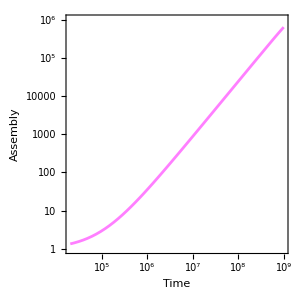

```mathematica
p3=LogLogPlot[Total@Table[ⅇ^a((If[a==0,1,nObj[a,α,κ,t]]With[{p=ToExpression["n"<>ToString[a]][t]},If[p>1,p-1,0]])/Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]],{a,0,25}]]),{a,0,25}],{t,Max@tDis,totalTime},Frame->True,FrameLabel->{"Time","Assembly"},AspectRatio->1,PlotStyle->{Magenta,Opacity[0.5]},PlotRange->{{Max@tDis,10^9},{1,10^6}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

#### Case 4: α=0.2

```mathematica
Clear[#]&/@Table["N"<>ToString[a],{a,0,25}];Clear[#]&/@Table["sol"<>ToString[a],{a,0,25}];Clear[α];
out4=solveEquations[{0.2,25,totalTime,10^5}];
```

```mathematica
solnList=ToExpression["N"<>ToString[#]]&/@Range[1,25];
```

```mathematica
tDis=Table[f[t_]=nObj[a,0.2,κ,t];t/.First@Solve[f[t]==1,t,Assumptions->{t>0&&t∈Reals}],{a,1,25}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Max@tDis
```

12500.

```mathematica
posPlot4=Flatten@Table[Block[{maxPos,val,pos},func[t_]=solnList[[i]];
maxPos=First@@Position[func["ValuesOnGrid"],Max[func["ValuesOnGrid"]]];
val=First@Nearest[func["ValuesOnGrid"][[1;;maxPos]],threshold];pos=Flatten@Position[func["ValuesOnGrid"],val];Flatten[func["Coordinates"]][[pos]]],{i,Length@solnList}];
```

```mathematica
Flatten@Position[Table[tDis[[i]]<posPlot4[[i]],{i,Length@posPlot4}],True]
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
thresholdList4=MapThread[{#1,#2}&,{Range[6,17],posPlot4[[6;;17]]}]
```

{{6,30187.},{7,111458.},{8,324380.},{9,834066.},{10,2.01188×10^6},{11,4.70364×10^6},{12,1.08578×10^7},{13,2.5046×10^7},{14,5.77461×10^7},{15,1.33946×10^8},{16,3.12146×10^8},{17,7.33346×10^8}}

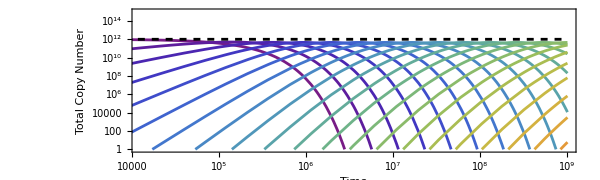

```mathematica
p41=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.2],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.2],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

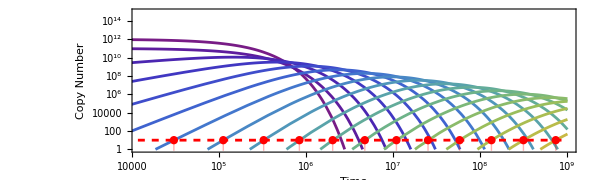

```mathematica
p42=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}],LogLogPlot[threshold,{t,0.001,totalTime},PlotStyle->{Red,Dashed},PlotRange->{{Max@tDis,10^9},{1,10^15}},AspectRatio->0.3],ListLogLogPlot[Evaluate[{#,threshold}&/@posPlot4[[6;;17]]],PlotStyle->{Red,PointSize[0.01]},Filling->Axis]},ImageSize->600]
```

```mathematica
colorStyle=Opacity[0.2,#]&/@Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]};
```

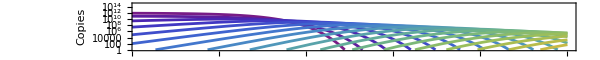

```mathematica
p43=LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.2_LongTime.png",p41,ImageResolution->300]; 
Export[baseDirectory<>"CopyNumber_alpha0.2_LongTime.png",p42,ImageResolution->300];
Export[baseDirectory<>"CopyNumber_alpha0.2_LongTime2.png",p43,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.2_LongTime.svg",p41]; 
Export[baseDirectory<>"CopyNumber_alpha0.2_LongTime.svg",p42];
Export[baseDirectory<>"CopyNumber_alpha0.2_LongTime2.svg",p43];
```

```mathematica
α=0.2;Table[ToExpression["n"<>ToString[a]][t_]=ToExpression["N"<>ToString[a]],{a,0,25}];
```

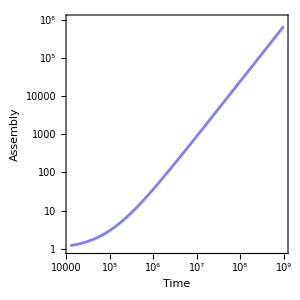

```mathematica
p4=LogLogPlot[Total@Table[ⅇ^a((If[a==0,1,nObj[a,α,κ,t]]With[{p=ToExpression["n"<>ToString[a]][t]},If[p>1,p-1,0]])/Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]],{a,0,25}]]),{a,0,25}],{t,Max@tDis,totalTime},Frame->True,FrameLabel->{"Time","Assembly"},AspectRatio->1,PlotStyle->{Blue,Opacity[0.5]},PlotRange->{{Max@tDis,10^9},{1,10^6}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

#### Case 5: α=0.001

```mathematica
Clear[#]&/@Table["N"<>ToString[a],{a,0,25}];Clear[#]&/@Table["sol"<>ToString[a],{a,0,25}];Clear[α];
out5=solveEquations[{0.001,25,totalTime,10^5}];
```

```mathematica
solnList=ToExpression["N"<>ToString[#]]&/@Range[1,25];
```

```mathematica
tDis=Table[f[t_]=nObj[a,0.001,κ,t];t/.First@Solve[f[t]==1,t,Assumptions->{t>0&&t∈Reals}],{a,1,25}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Max@tDis
```

10010.

```mathematica
posPlot5=Flatten@Table[Block[{maxPos,val,pos},func[t_]=solnList[[i]];
maxPos=First@@Position[func["ValuesOnGrid"],Max[func["ValuesOnGrid"]]];
val=First@Nearest[func["ValuesOnGrid"][[1;;maxPos]],threshold];pos=Flatten@Position[func["ValuesOnGrid"],val];Flatten[func["Coordinates"]][[pos]]],{i,Length@solnList}];
```

```mathematica
Flatten@Position[Table[tDis[[i]]<posPlot5[[i]],{i,Length@posPlot5}],True]
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}

```mathematica
thresholdList5=MapThread[{#1,#2}&,{Range[6,17],posPlot4[[6;;17]]}]
```

{{6,30187.},{7,111458.},{8,324380.},{9,834066.},{10,2.01188×10^6},{11,4.70364×10^6},{12,1.08578×10^7},{13,2.5046×10^7},{14,5.77461×10^7},{15,1.33946×10^8},{16,3.12146×10^8},{17,7.33346×10^8}}

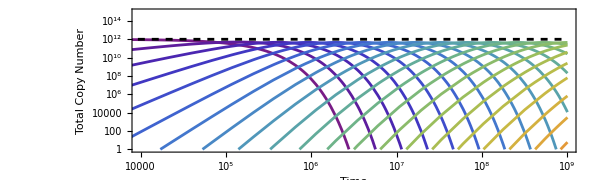

```mathematica
p51=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.001],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.001],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

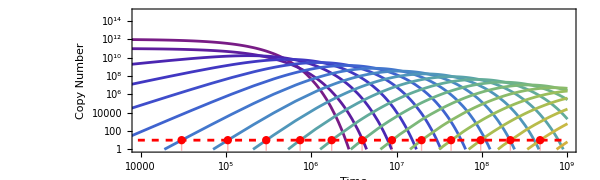

```mathematica
p52=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copy Number"},AspectRatio->0.3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}],LogLogPlot[threshold,{t,0.001,totalTime},PlotStyle->{Red,Dashed},PlotRange->{1,10^15},AspectRatio->0.3],ListLogLogPlot[Evaluate[{#,threshold}&/@posPlot5[[6;;17]]],PlotStyle->{Red,PointSize[0.01]},Filling->Axis]},ImageSize->600]
```

```mathematica
colorStyle=Opacity[0.2,#]&/@Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]};
```

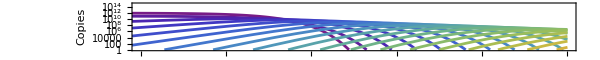

```mathematica
p53=LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.001_LongTime.png",p51,ImageResolution->300]; 
Export[baseDirectory<>"CopyNumber_alpha0.001_LongTime.png",p52,ImageResolution->300];
Export[baseDirectory<>"CopyNumber_alpha0.001_LongTime2.png",p53,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.001_LongTime.svg",p51]; 
Export[baseDirectory<>"CopyNumber_alpha0.001_LongTime.svg",p52];
Export[baseDirectory<>"CopyNumber_alpha0.001_LongTime2.svg",p53];
```

```mathematica
α=0.001;Table[ToExpression["n"<>ToString[a]][t_]=ToExpression["N"<>ToString[a]],{a,0,25}];
```

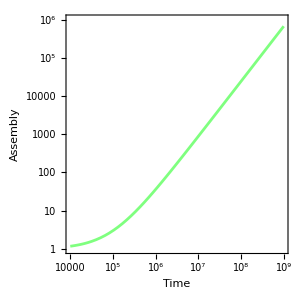

```mathematica
p5=LogLogPlot[Total@Table[ⅇ^a((If[a==0,1,nObj[a,α,κ,t]]With[{p=ToExpression["n"<>ToString[a]][t]},If[p>1,p-1,0]])/Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]],{a,0,25}]]),{a,0,25}],{t,Max@tDis,totalTime},Frame->True,FrameLabel->{"Time","Assembly"},AspectRatio->1,PlotStyle->{Green,Opacity[0.5]},PlotRange->{{Max@tDis,10^9},{1,10^6}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

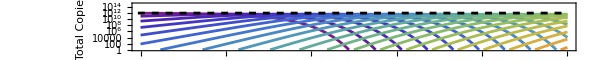

```mathematica
totalCopies=Show[{LogLogPlot[Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.001],{a,0,25}]],{t,Max@tDis,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->Flatten@Thread@{ColorData["Rainbow"]/@Range[0,1,1/25]},Frame->True,FrameLabel->{"Time","Total Copies"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->600],
LogLogPlot[Total@Evaluate[Table[ToExpression["N"<>ToString[a]],{a,0,25}]Table[If[a==0,1,nObj[a,α,κ,t]/.α->0.001],{a,0,25}]],{t,0.001,totalTime},PlotRange->{{Max@tDis,10^9},{1,10^15}},PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{"Time","Total Copy Number"},AspectRatio->0.1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}]},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.001_LongTime2.png",totalCopies,ImageResolution->300];
```

```mathematica
Export[baseDirectory<>"TotalCopyNumber_alpha0.001_LongTime2.svg",totalCopies,ImageResolution->300];
```

Plotting all the assembly together,

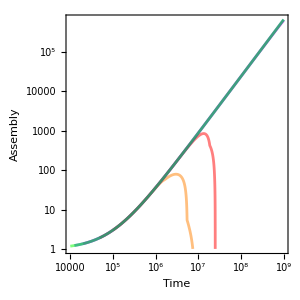

```mathematica
Show[{p1,p2,p3,p4,p5},PlotRange->Full]
```

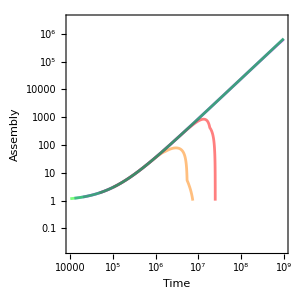

```mathematica
Assembly=Show[{p1,p2,p3,p4,p5},PlotRange->{-4,15}]
```

```mathematica
legends=LineLegend[{Orange,Red,Magenta,Blue,Green},{1.0,0.8,0.5,0.2,0.001},LegendLabel->"α",Spacings->0.25]
```

```mathematica
Export[baseDirectory<>"Assembly_DP.png",Assembly,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/Assembly_DP.png

```mathematica
Export[baseDirectory<>"Assembly_DP.svg",Assembly]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/Assembly_DP.svg

```mathematica
Export[baseDirectory<>"legends.png",legends,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/legends.png

```mathematica
Export[baseDirectory<>"legends.svg",legends,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/legends.png

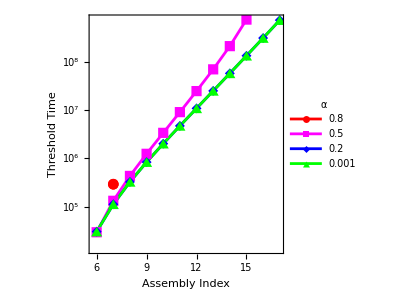

```mathematica
pThresh=ListLogPlot[{thresholdList2,thresholdList3,thresholdList4,thresholdList5},Joined->True,PlotStyle->{Red,Magenta,Blue,Green},PlotMarkers->Automatic,Frame->True,FrameLabel->{"Assembly Index","Threshold Time"},PlotLegends->Placed[LineLegend[{"0.8","0.5","0.2","0.001"},LegendLabel->"α",Spacings->0.25,LegendFunction->"Frame"],{0.75,0.3}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"Time_Threshold.png",pThresh,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/Time_Threshold.png

```mathematica
Export[baseDirectory<>"Time_Threshold.svg",pThresh]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/Time_Threshold.svg

We assume there is a minimum threshold in copy number for a discovered object to be “observed”.

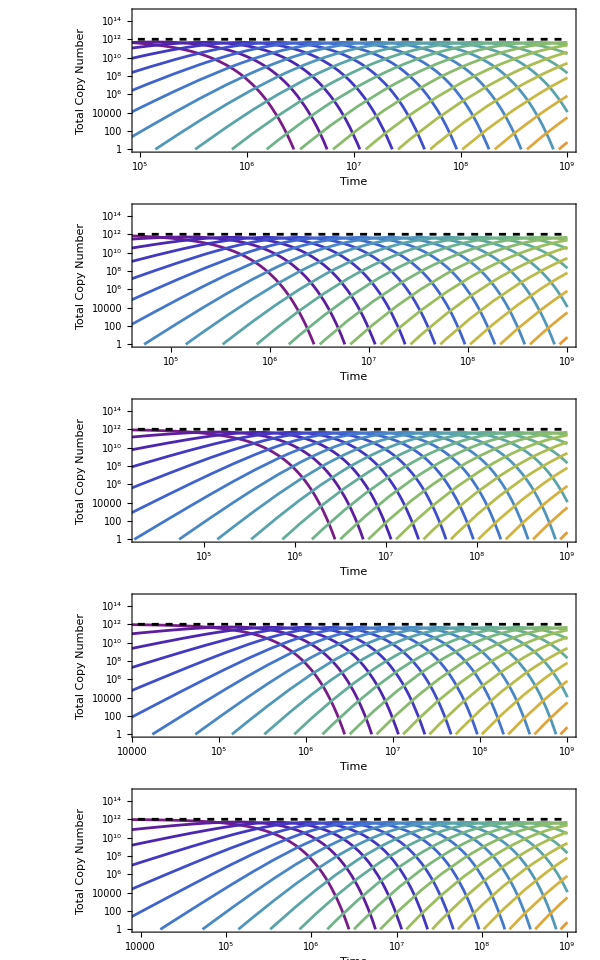

```mathematica
GraphicsColumn[{p11,p21,p31,p41,p51},ImageSize->600]
```

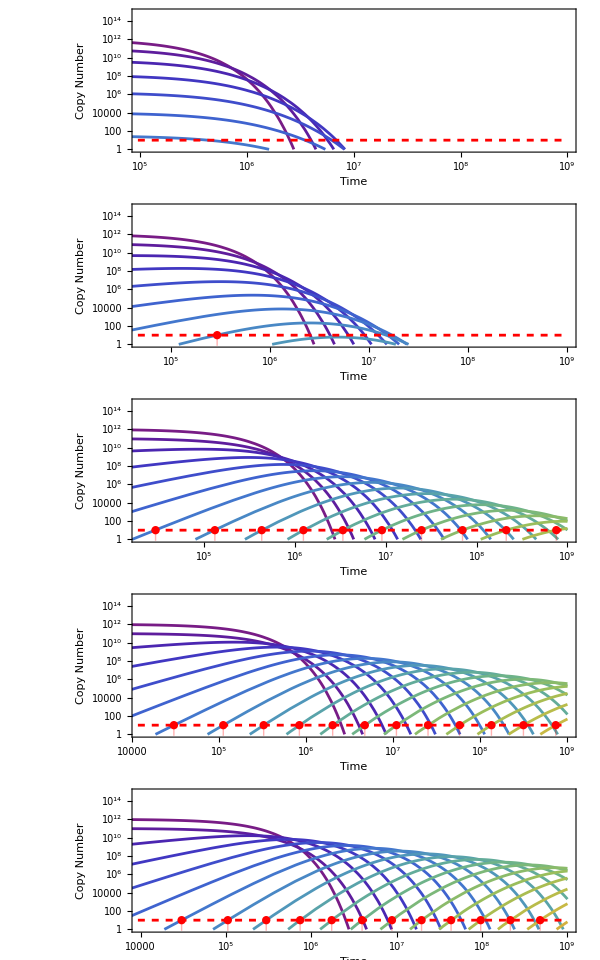

```mathematica
GraphicsColumn[{p12,p22,p32,p42,p52},ImageSize->600]
```